# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
sims = SemanticImport[FileNameJoin[{NotebookDirectory[],"MH_data.txt"}]];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport[FileNameJoin[{NotebookDirectory[],"CDF_data.txt"}]];
```

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,250^α/2];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,250^α/2];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,250^α/2];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(1/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(2 π(Dα/μ)^(1/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,250^α/2];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

(α-1)+O[α-1]^2

```mathematica
exphom[x_,coal_,μ_,Dα_:250^2/2]:=Exp[-√(μ/Dα)x]/(1+4√(μ Dα)/coal)
```

```mathematica
xlist=10^Range[-6,3.5,.25];
```

```mathematica
xlist
```

{1.×10^-6,1.77828×10^-6,3.16228×10^-6,5.62341×10^-6,0.00001,0.0000177828,0.0000316228,0.0000562341,0.0001,0.000177828,0.000316228,0.000562341,0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[Cos[k x]/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlist⟦;;-2⟧}]];
```

```mathematica
xmaxes=AssociationThread[αlist,{6400,3200,1600,400,200,100,30,20,8}];
```

# Plots

## α=0.5

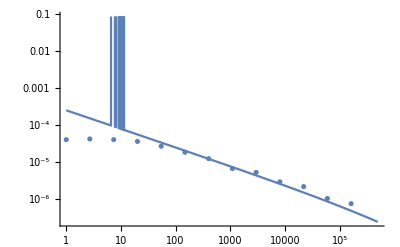

```mathematica
Module[{α=0.5, coal=0.01, μ = 0.001, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coal/2 fLT[x,μ,α],{x,1, 5 10^5}],
PlotRange->All]]
```

```mathematica
(* note that coal here is 1/rho, i.e. 1 over the population density*)
```

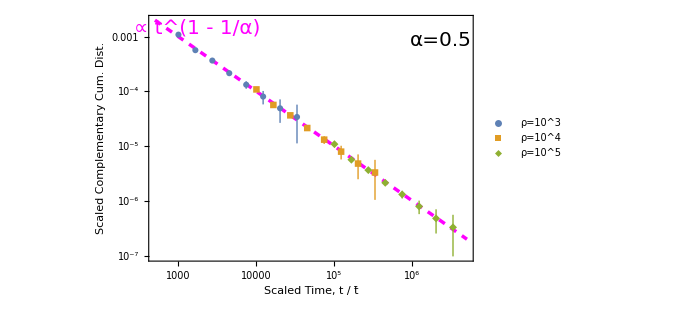

```mathematica
Module[{α=0.5, coal=.001, plotcdf, c =1, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->maxcdf*#coal/.001 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->3.141*((1/α -1)/(Gamma[1/α +1]))*#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfLow|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfHigh|>&];
dummy= dummy[Select[#T < 50 &]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[x^(1-1/α),{x,500,5000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.15,.95}]] },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
maxcdf
```

0.000693185

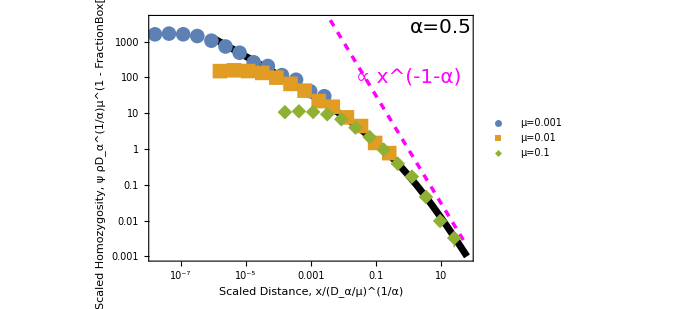

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.8,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Homozygosity, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

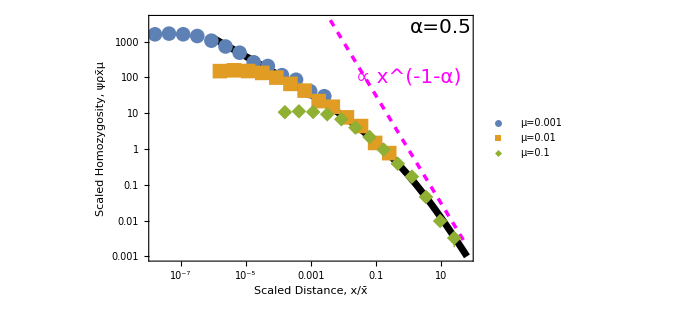

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.8,.75}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

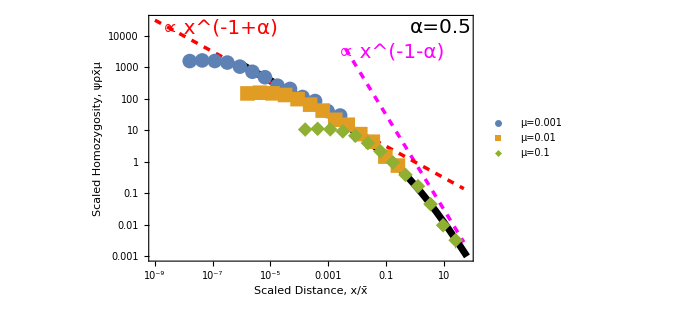

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[x^(-1+α),{x,.000000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.22,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.75,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

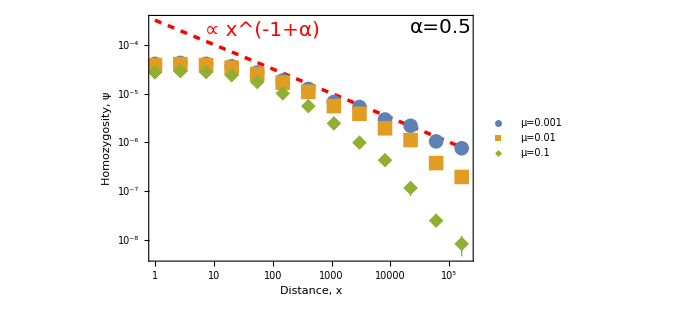

```mathematica
Module[{α=0.5,D = (250)^(2), coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*coal*D))*x^(-1+α),{x,1,200000},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style[" ∝ x^(-1+α) ",Red,20],Scaled[{.35,.94}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

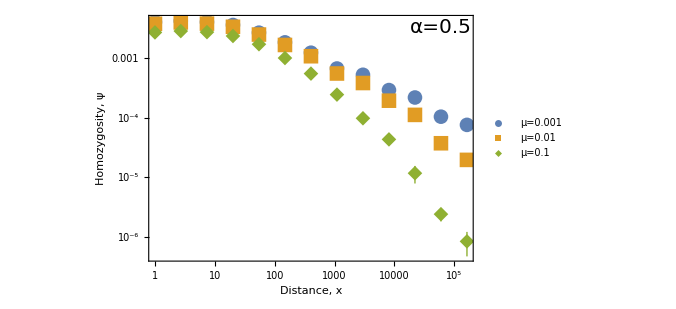

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False ]]
```

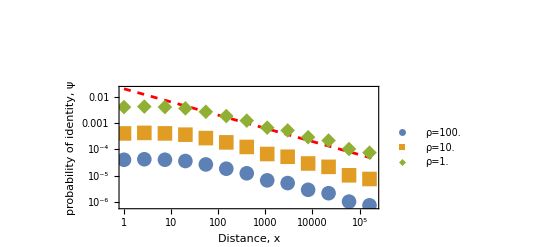

```mathematica
Module[{α=0.5,μ =0.001, plotpoints,coalvals=coallist⟦;;3⟧,yscale=80000},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{coal,coalvals}];
Show[LogLogPlot[.02*x^(-1+α),{x,1,200000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@(coalvals^-1),{.2,.3}]],Epilog->{Text[Style["α=0.5",20],{5,7}],Text[Style["x^(-1-α)",Magenta,20],{0,4}]},goodlabel["Distance, x","probability of identity, ψ",20],FrameStyle->Directive[20,Black],
PlotRange->All,Axes->False]]
```

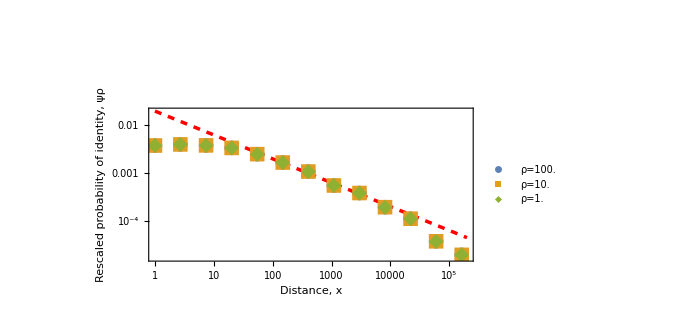

```mathematica
Module[{α=0.5,μ =0.01, plotpoints,coalvals=coallist⟦;;3⟧,yscale=80000},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]/(#coal)}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{coal,coalvals}];
Show[LogLogPlot[.02*x^(-1+α),{x,1,200000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@(coalvals^-1),{.2,.3}]],Epilog->{Text[Style["α=0.5",20],{5,7}],Text[Style["x^(-1-α)",Magenta,20],{0,4}]},goodlabel["Distance, x","Rescaled probability of identity, ψρ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=.75

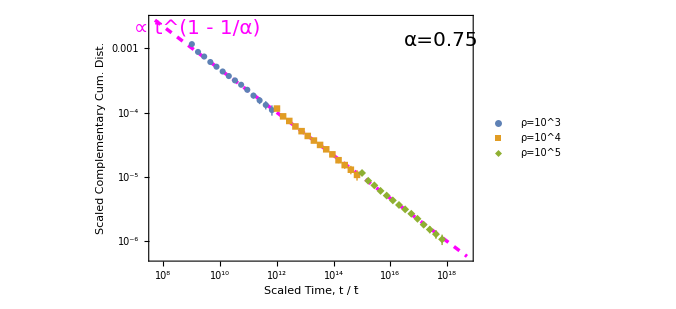

```mathematica
Module[{α=0.75, coal=.001, plotcdf, c =1, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->maxcdf*#coal/.001 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->3.141*((1/α -1)/(Gamma[1/α +1]))*#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfHigh|>&];
dummy= dummy[Select[#T < 1000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[x^(1-1/α),{x,50000000,5000000000000000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.75",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.15,.95}]] },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

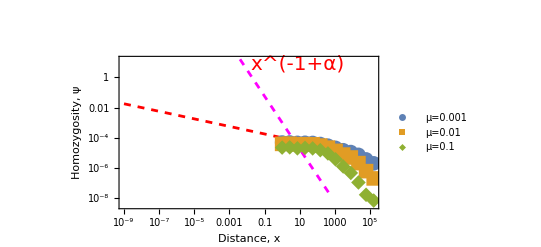

```mathematica
Module[{α=0.75,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[.001*x^(-1-α),{x,.004,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[.0001*x^(-1+α),{x,.000000001,500},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.75",20],{2,8}],Text[Style["x^(-1+α)",Red,20],{2,2}], Text[Style["x^(-1-α)",Magenta,20],{0,5}]},goodlabel["Distance, x","Homozygosity, ψ ",20],FrameStyle->Directive[20,Black], 
PlotRange->All,Axes->False]]
```

## α=1

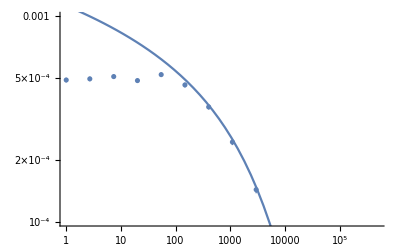

```mathematica
Module[{α=1.0, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[.05fLT[x,μ,α],{x,1, 5 10^5}],
PlotRange->{All,{-4,-3}Log[10]}]]
```

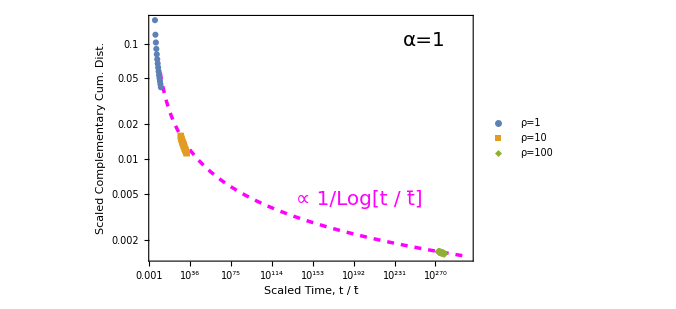

```mathematica
Module[{α=1.00, coal=1, plotcdf, c =1, D =1},
dummy= cdfsims[Select[#alpha == α && #coal ≥ .001*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(D*Exp[2*Pi/#coal])*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#coal*#compcdf/(2*Pi*D)|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#coal*#dcdfLow/(2*Pi*D)|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#coal*#dcdfHigh/(2*Pi*D)|>&];
dummy= dummy[Select[#T < 500000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{ 1, .1, .01}}];



Show[LogLogPlot[1/Log[x],{x,10^1,10^300},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{ "1", "10", "100"},Scaled[{.2,.2}]]],Epilog->{Text[Style["α=1",20],Scaled[{.85,.9}]],Text[Style["∝ 1/Log[t / t̄]",Magenta,20],Scaled[{.65,.25}]], ImageSize->500 },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black],ImageSize->500,
PlotRange->All,Axes->False]]
```

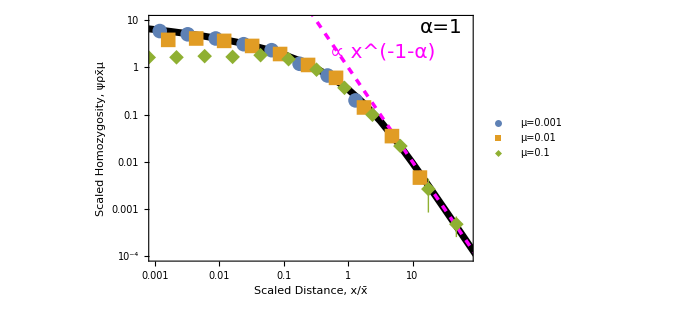

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦;;3⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,70},{10^-4,10}}] ,
LogLogPlot[x^(-1-α),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.72,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

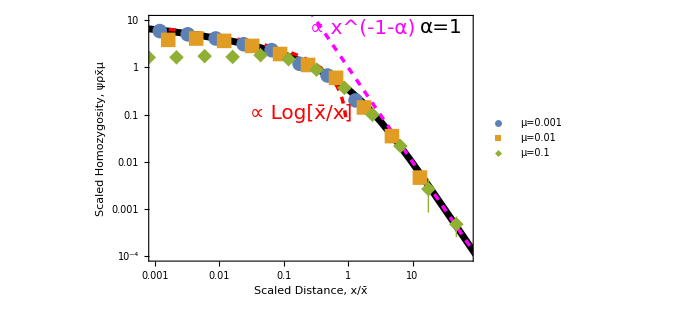

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦;;3⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,70},{10^-4,10}}], LogLogPlot[Log[1/x],{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
LogLogPlot[x^(-1-α),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.66,.95}]], Text[Style["∝ Log[x̄/x]",Red,20],Scaled[{0.47,.6}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α = 1.25

```mathematica
250^1.25/2
```

497.044

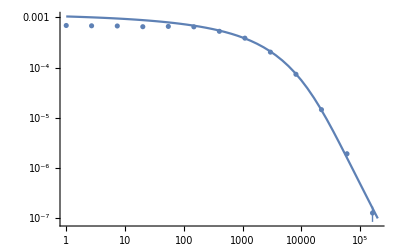

```mathematica
Module[{α=1.25, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],PlotRange->All]]
```

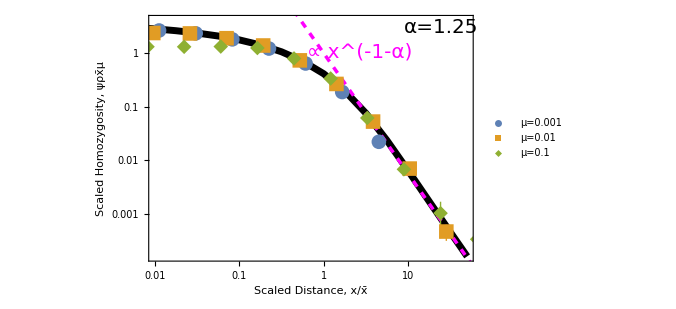

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.65,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

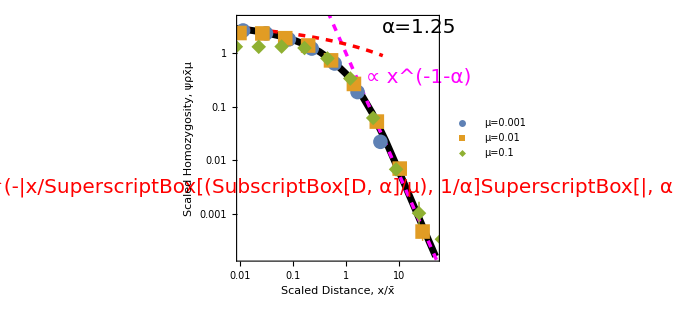

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[4*Exp[-x^(α-1)],{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.45

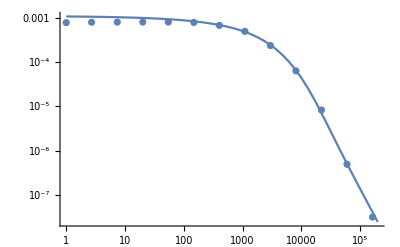

```mathematica
Module[{α=1.45, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],
PlotRange->All]]
```

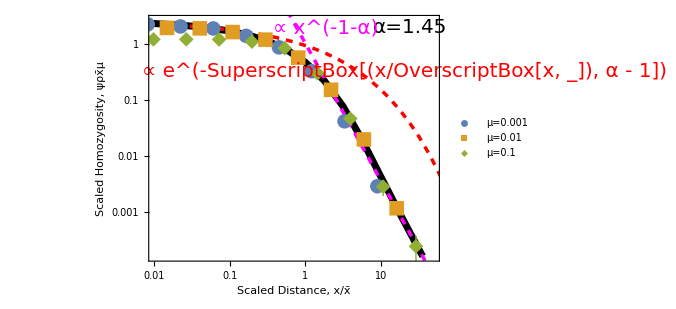

```mathematica
Module[{α=1.45,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[2.5*Exp[-x^(α-1)],{x,.001,5000},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.61,.95}]], Text[Style["∝ e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])",Red,20],Scaled[{0.88,.77}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

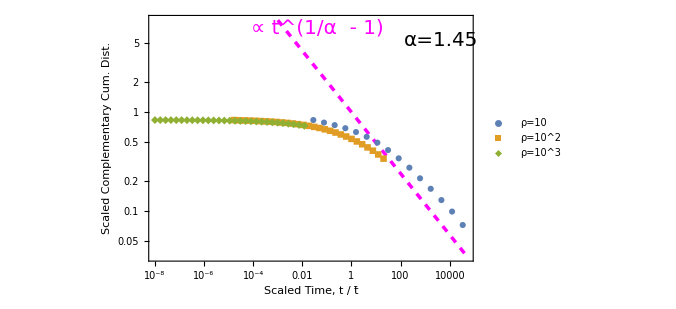

```mathematica
Module[{α=1.45, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.52,.95}]] },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=1.65

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand (0.31831 Cos[1.00024 k])/(0.01+4524.5 (0.+k)^1.65) over {0,∞}. DoubleExponentialOscillatory obtained 0.0238148 and 2.01953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {283.95}. NIntegrate obtained 0.0238146 and 5.71187×10^-7 for the integral and error estimates.

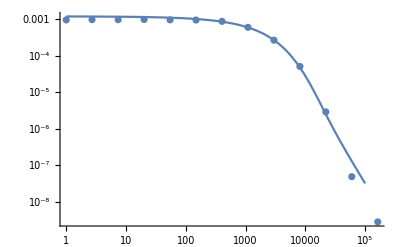

```mathematica
Module[{α=1.65, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 10^5}],
PlotRange->All]]
```

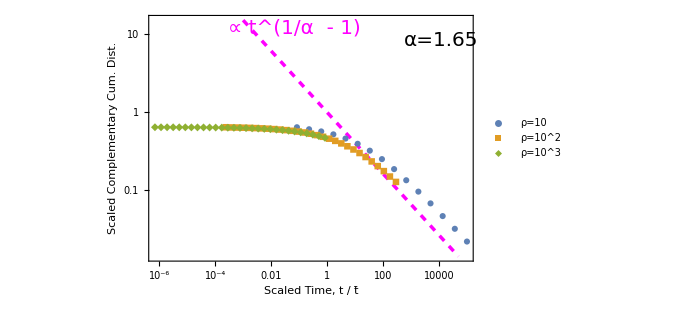

```mathematica
Module[{α=1.65, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.45,.95}]] },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

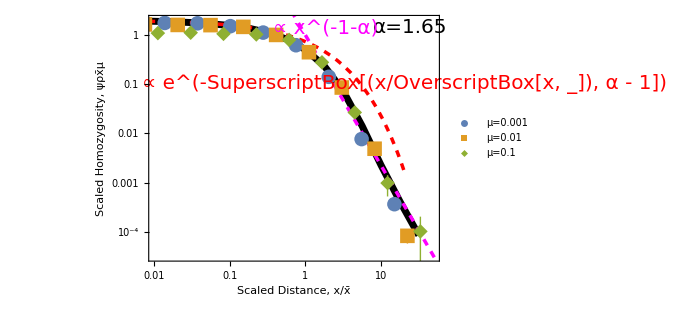

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤3*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4.5,All}}], LogLogPlot[2*Exp[-x^(α-1)],{x,.001,20},PlotStyle->{Red,Dashed,Thickness[.005]}],
LogLogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]], Text[Style["∝ e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])",Red,20],Scaled[{0.88,.72}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.61,0.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

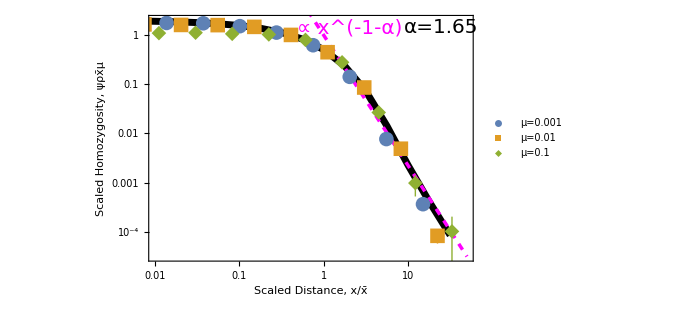

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤1000*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4.5,All}}],
LogLogPlot[x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.62,0.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

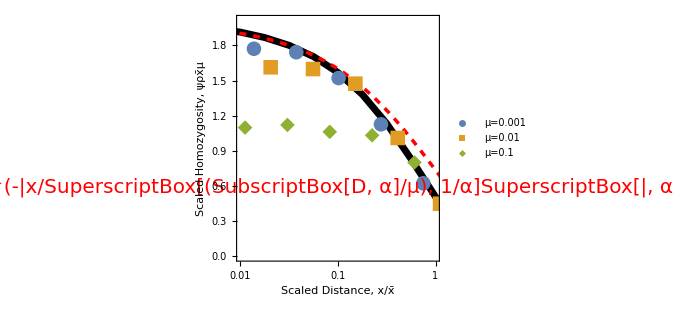

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLinearPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1},{10^-6,All}}], LogLinearPlot[2*Exp[-x^(α-1)],{x,.0001,10},PlotStyle->{Red,Dashed,Thickness[.005]}],
LogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLinearPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],{3,1}], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],{0.6,0.8}]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.85

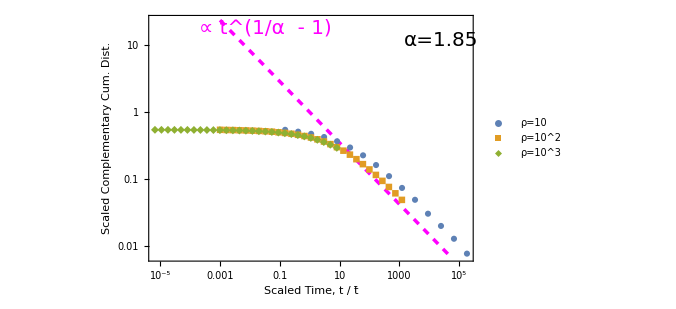

```mathematica
Module[{α=1.85, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.36,.95}]] },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

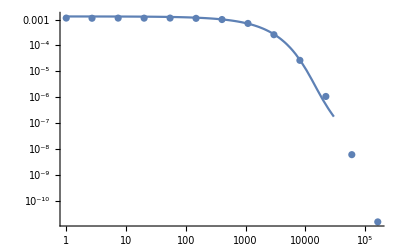

```mathematica
Module[{α=1.85, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 3 10^4}],
PlotRange->All]]
```

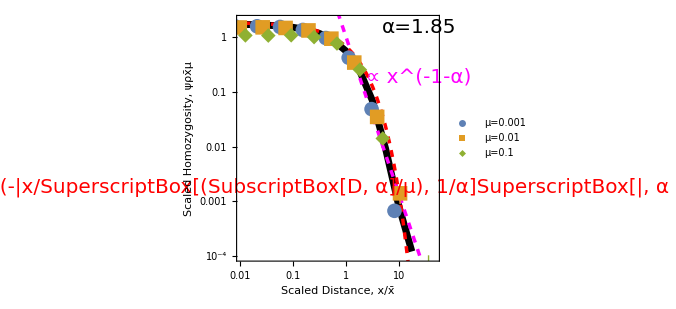

```mathematica
Module[{α=1.85,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4,2}}],
LogLogPlot[x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[1.8*Exp[-x^(α-1)],{x,.001,500000},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.48,.3}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=2.05 (F distribution)

Null

```mathematica
df =0.5Module[{α=2.05},Moment[FRatioDistribution[2α,2α],2]]
```

59.5476

```mathematica
250^2.05/2
```

41185.8

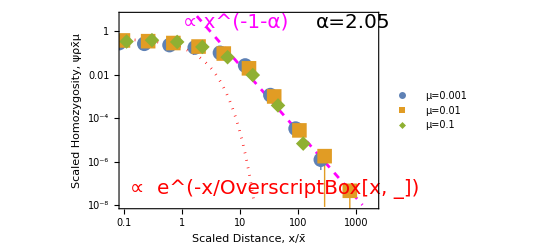

```mathematica
Module[{α=2.05,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/(√(df/#mu)),Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,2,df]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[
LogLogPlot[{30*x^(-1-α), 2*(1*.1*Sqrt[125/.1])/(1+1*4*Sqrt[125*.1])*Exp[-x]},{x,.01,2000},PlotStyle->{{Magenta,Dashed,Thickness[.005]},{Red,Dotted,Thickness[.005]}},PlotRange->{{.1,2000},{10^-8,5}}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.45,0.95}]],
Text[Style["  ∝  e^(-x/OverscriptBox[x, _])",Red,20],Scaled[{.60,.1}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black]]]
```

## All

We can kind of rescale everything away, but there should be and is some residual alpha dependence. μ=1 looks weird.

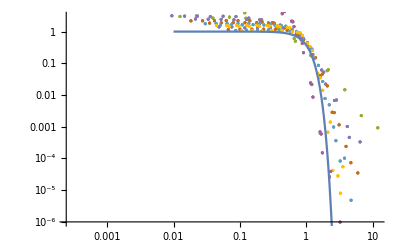

```mathematica
Module[{ plotpoints},plotpoints =Table[{((#x0)/xscale[#mu,#alpha])^(1/(1+#alpha)),Around[#hom,{#dhomLow,#dhomHigh}]/homscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha==α&&#mu<1&&#x0>0&&#hom>0&]],{α,αlist}];
Show[ListLogLogPlot[plotpoints,PlotRange->{All,{10^-6,3}},IntervalMarkersStyle->{"FenceWidth"->Thick}],
LogLogPlot[Exp[-x^3],{x,.01,100}]]]
```

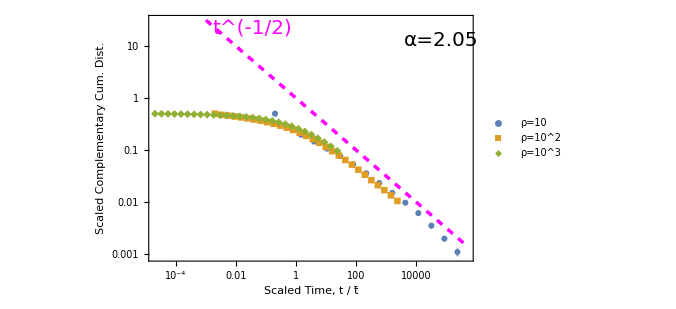

```mathematica
Module[{α=2.05, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-2)*D)^(1/(1 - 2))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(2*Sin[Pi/2])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(2*Sin[Pi/2])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(2*Sin[Pi/2])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(-1/2),{x,.001,500000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.9}]],Text[Style["t^(-1/2)",Magenta,20],Scaled[{.32,.95}]] },goodlabel["Scaled Time, t / t̄","Scaled Complementary Cum. Dist.",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

# Math

```mathematica
lineStyle={Thick,Black,Dashed};
```

```mathematica
lineStyle2={Thick, Black};
```

```mathematica
lineStyle3={Thick, Blue};
```

```mathematica
lineStyle4={Thick,Green};
```

```mathematica
lineStyle5={Thick,Red};
```

```mathematica
lineStyle6={Thick,Purple};
```

```mathematica
lineStyle7={Thick,Yellow};
```

```mathematica
lineStyle8={Thick,White};
```

```mathematica
line99=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line0=Line[{{0,0},{0,2}}];
```

```mathematica
line1=Line[{{1,0},{1,1}}];
```

```mathematica
line2=Line[{{2,0},{2,1}}];
```

```mathematica
line3=Line[{{3,0},{3,2}}];
```

```mathematica
line999=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line00=Line[{{0,0},{0,2}}];
```

```mathematica
line11=Line[{{1,1},{1,2}}];
```

```mathematica
line22=Line[{{2,0},{2,2}}];
```

```mathematica
line33=Line[{{3,0},{3,2}}];
```

```mathematica
line44=Line[{{0,2},{3,2}}];
```

```mathematica
line55=Line[{{0,0},{3,0}}];
```

```mathematica
line66=Line[{{0,1},{3,1}}];
```

```mathematica
line77=Line[{{0,.5},{1,.5}}];
```

```mathematica
line88=Line[{{0,.5},{3,.5}}];
```

```mathematica
line999=Line[{{-.5,0},{-.5,-2}}];
```

```mathematica
line000=Line[{{0,0},{0,-2}}];
```

```mathematica
line111=Line[{{1,0},{1,-1}}];
```

```mathematica
line222=Line[{{2,0},{2,-1}}];
```

```mathematica
line333=Line[{{3,0},{3,-2}}];
```

```mathematica
line444=Line[{{0,-2},{3,-2}}];
```

```mathematica
line555=Line[{{0,0},{3,0}}];
```

```mathematica
line666=Line[{{0,-1},{3,-1}}];
```

```mathematica
line777=Line[{{0,.3},{1,.3}}];
```

```mathematica
line888=Line[{{0,.3},{3,.3}}];
```

```mathematica
line999=Line[{{0,0},{3,0}}];
```

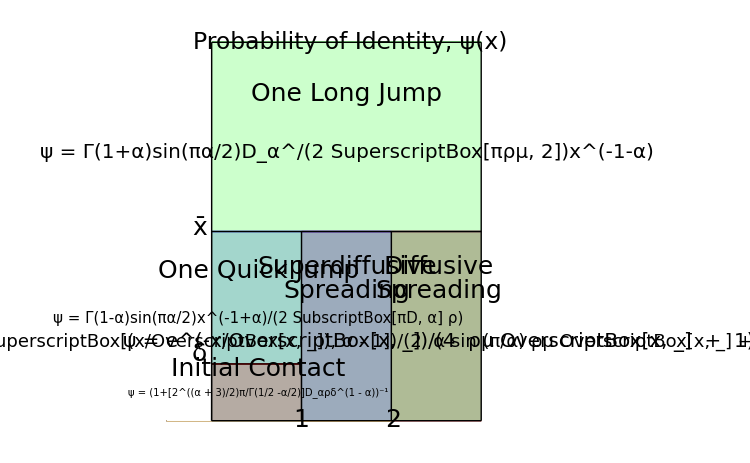

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .3*UnitStep[x] -.3*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]},{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7], Directive[lineStyle8],Directive[lineStyle8]},Epilog->{Directive[lineStyle2],Text[Style["1",Black,25],Scaled[{.43,.020}]],Text[Style["2",Black,25],Scaled[{.71,.020}]], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,25],Scaled[{.57,.85}]],Text[Style["ψ = Γ(1+α)sin(πα/2)D_α^/(2 SuperscriptBox[πρμ, 2])x^(-1-α)",Black,20],Scaled[{.57,.70}]],  Text[Style["Superdiffusive",Black,25],Scaled[{.57,.41}]], Text[Style[" Spreading",Black,25],Scaled[{.57,.35}]],Text[Style["ψ=e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])/(2  α sin (π/α) ρμ OverscriptBox[x, _] + 1)",Black,18],Scaled[{.57,.22}]], Text[Style["One Quick Jump",Black,25],Scaled[{.3,.40}]],Text[Style["ψ = Γ(1-α)sin(πα/2)x^(-1+α)/(2 SubscriptBox[πD, α] ρ)",Black,15],Scaled[{.30,.28}]] ,Text[Style["ψ = (1+[2^((α + 3)/2)π/Γ(1/2 -α/2)]D_αρδ^(1 - α))^-1",Black,10],Scaled[{.3,.09}]],Text[Style["Initial Contact",Black,25],Scaled[{.30,.15}]] ,Text[Style[" ψ = e^(-x/OverscriptBox[x, _])/(4  ρμ OverscriptBox[x, _]  +  1)",Black,20],Scaled[{.85,.22}]], Text[Style["Probability of Identity, ψ(x) ",Black,23.5],Scaled[{.58,.98}]],Text[Style["Diffusive",Black,25],Scaled[{.85,.41}]],Text[Style[" Spreading",Black,25],Scaled[{.85,.35}]],line0, line1, line2, line3, line44, line66, line777, line999}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

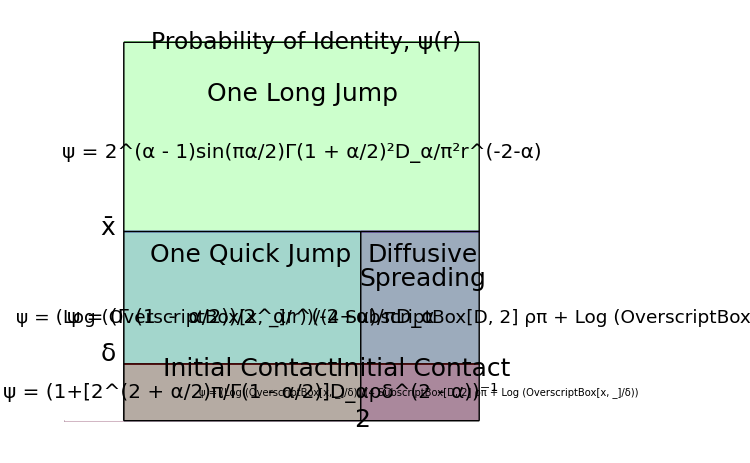

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .3*UnitStep[x], UnitStep[x -2], 0, 0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,25],Scaled[{.57,.85}]],Text[Style["ψ = 2^(α - 1)sin(πα/2)Γ(1 + α/2)^2D_α/π^2r^(-2-α) ",Black,20],Scaled[{.57,.70}]],   Text[Style["One Quick Jump",Black,25],Scaled[{.45,.44}]],Text[Style["ψ = (Γ (1  -  α/2))/2^αr^(-2+α)/πD_α",Black,20],Scaled[{.45,.28}]], Text[Style["ψ = (1+[2^(2 + α/2)π/Γ(1 - α/2)]D_αρδ^(2 - α))^-1",Black,20],Scaled[{.45,.09}]],Text[Style["ψ = (Log (OverscriptBox[x, _]/r))/(4 SubscriptBox[D, 2] ρπ + Log (OverscriptBox[x, _]/δ))",Black,18.5],Scaled[{.85,.28}]], Text[Style["Diffusive",Black,25],Scaled[{.85,.44}]],Text[Style["Spreading",Black,25],Scaled[{.85,.38}]], Text[Style["Initial Contact",Black,25],Scaled[{.45,.15}]],Text[Style[" ψ = (Log (OverscriptBox[x, _]/δ))/(4 SubscriptBox[D, 2] ρπ + Log (OverscriptBox[x, _]/δ))",Black,10],Scaled[{.84,.09}]],Text[Style["Initial Contact",Black,25],Scaled[{.85,.15}]],Text[Style[" 2 ",Black,25],Scaled[{.71,.020}]], Text[Style["Probability of Identity, ψ(r) ",Black,23.5],Scaled[{.58,.98}]],line0, line2, line3, line44, line55, line66, line888}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

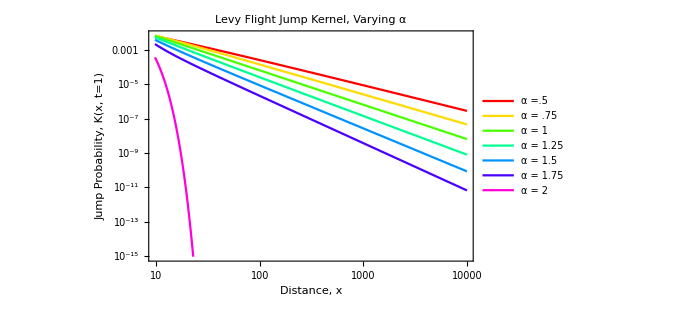

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],x],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{x,0,10000}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Levy Flight Jump Kernel, Varying α", FontSize -> 24], PlotLegends->{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"}, Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Distance, x","Jump Probability, K(x, t=1)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

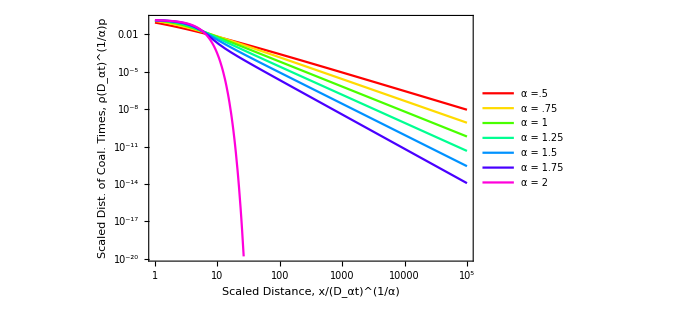

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],xdimensionless],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{xdimensionless,1,10^5}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[ Black], PlotLabel -> Style["", FontSize -> 18], PlotLegends->Placed[{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"},{0.15,0.4}], Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Scaled Distance, x/(D_αt)^(1/α)","Scaled Dist. of Coal. Times, ρ(D_αt)^(1/α)p",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,PlotRangePadding->Scaled[.06],Axes->False]
```

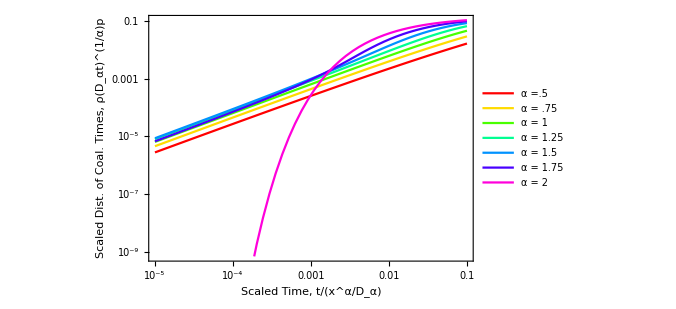

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],(timedimensionless)^(-1/(α +1))],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{timedimensionless,10^-5,10^-1}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[ Black], PlotLabel -> Style["", FontSize -> 18], PlotLegends->Placed[{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"},{0.9,0.4}], Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Scaled Time, t/(x^α/D_α)","Scaled Dist. of Coal. Times, ρ(D_αt)^(1/α)p",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,PlotRangePadding->Scaled[.06],Axes->False]
```